-Graphics-

## Lesson 4: Classification of differential equations

-Graphics-

## Overview

Differential equations take many forms and can include functions of many variables:

y''(t)+y'(t)=y(t)

(∂y(x,t))/(∂x^2)+(∂y(x,t))/(∂t^2)+sin(x)=0

This lesson will discuss the methods of defining, solving and plotting general differential equations in the Wolfram Language.

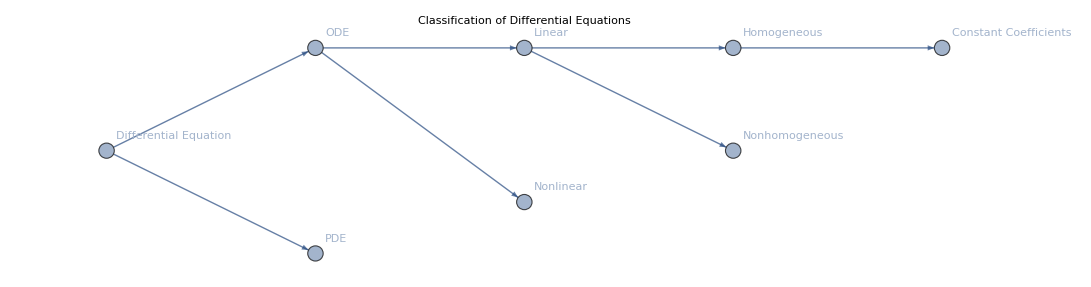

```mathematica
Graph[{1->2,2->5,1->3,4->7,2->4,4->6,6->8},]
```

## Ordinary Differential Equations

With ordinary differential equations (ODEs), only ordinary derivatives appear in the differential equation, and the unknown function depends on a single independent variable.

Examples include:

y'(t)=y(t)

f'(x)*x=sin(x)

g''(t)+g'(t)=g(t)

In order to solve an ordinary differential equation, use the Wolfram Language function DSolveValue:

```mathematica
DSolveValue[{y'[t]==y[t],y[0]==1},y[t],t]
```

ⅇ^t

Solutions to seemingly simple differential equations can sometimes have very complicated answers or may not even exist.

## Finding Solutions

Begin with the initial value problem for an ordinary differential equation:

x f''(x)=x^2

f(0)=0

f'(0)=5

Use DSolveValue to find a solution:

```mathematica
sln=DSolveValue[{x f''[x]==x^2,f[0]==0,f'[0]==5},f[x],x]
```

1/6 (30 x+x^3)

The solution to the differential equation is now stored in the variable sln, which makes it easy to apply Plot to the solution:

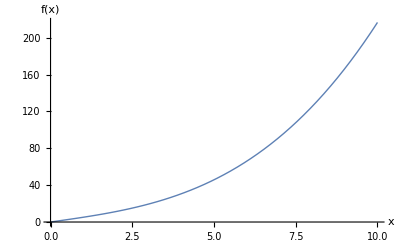

```mathematica
Plot[sln,{x,0,10},]
```

In order to verify that the solution is correct, use the function Simplify:

```mathematica
Simplify[x D[sln,x,x]==x^2]
```

True

## Finding Solutions

Study another initial value problem:

f''(x)=-f(x)

f(0)=0

f'(0)=5

Find the solution using DSolveValue:

```mathematica
sln=DSolveValue[{f''[x]==-f[x],f[0]==0,f'[0]==5},f[x],x]
```

5 Sin[x]

Apply Plot to the solution:

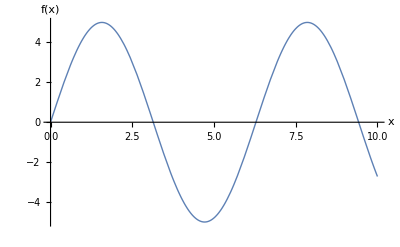

```mathematica
Plot[sln,{x,0,10},]
```

In order to verify that the solution is correct, use the function Simplify:

```mathematica
Simplify[D[sln,x,x]==-sln]
```

True

## Partial Differential Equations

With partial differential equations (PDEs), partial derivatives appear in the differential equation.

The unknown function depends on multiple independent variables.

Examples of PDEs are:

(∂^2 y(x,t))/(∂x∂t)+(∂^2 y(x,t))/(∂t^2)+sin(x t)=0

(∂^2 f(x,y))/(∂x^2)+(∂^2 f(x,y))/(∂y^2)+y+x f(x,y)=0

(∂y(x,t))/(∂x)+(∂y(x,t))/(∂t)=0

DSolveValue can be used to solve many types of partial differential equations.

The theory of partial differential equations is not as well understood as that of ordinary differential equations and thus plays a minor role in this course.

## Partial Differential Equations

Observe a problem for a partial differential equation:

(∂u(x,t))/(∂x)+(∂u(x,t))/(∂t)=0

u(x,0)=sin(x)

u(0,t)=0

Begin by specifying the equation and the conditions the solution must satisfy:

```mathematica
eqn=D[u[x,t],x]+D[u[x,t],t]==0;
ibc={u[x,0]== Sin[x],u[0,t]==0};
sln=DSolveValue[{eqn,ibc},u[x,t],{x,t}]//FullSimplify
```

(-1+HeavisideTheta[t-x]) Sin[t-x]

Use Plot3D to visualize the solution from DSolveValue:

```mathematica
Plot3D[sln,{t,0,1},{x,0,1},]
```

-Graphics3D-

## Order

The order of a differential equation is the order of the highest derivative that appears in the equation.

For example, the following is a second-order differential equation:

y''(t)+5 y'(t)+y(t)=sin(t)

This can be written in the Wolfram Language as:

```mathematica
y''[t]+5y'[t]+y[t]==Sin[t]
```

y[t]+5 y'[t]+y''[t]==Sin[t]

The next differential equation is a fifth-order differential equation:

y^(5)(t) y^(2)(t)=e^(t^2)

This can be written in the Wolfram Language as:

```mathematica
D[y[t],{t,5}] D[y[t],{t,2}]==Exp[t^2]
```

y''[t] y^(5)[t]==ⅇ^(t^2)

## Linear and Nonlinear Equations

An ordinary differential equation is said to be linear if it can be written in the form:

a_n(t)(ⅆ^n y(t))/(ⅆ t^n)+...+a_1(t)(ⅆy(t))/ⅆt+a_0(t)y(t)=g(t)

where the a_i(t) and g(t) are arbitrary differentiable functions that do not need to be linear.

Mathematical theory and methods for solving linear equations are highly developed and will be the main focus of the course.

An ordinary differential equation is said to be nonlinear if it cannot be written in a linear form.

For example, the following are examples of linear differential equations:

y'(t)=5y(t)

f''(x)+3f'(x)x=sin(x)

While this equation is nonlinear due to the product of the derivative terms and y(t) being squared:

y''(t)y'(t)+(y(t))^2=1

## Classifications of Linear Equations

As stated, an ordinary differential equation is said to be linear if it can be written in the form:

a_n(t)(ⅆ^n y(t))/(ⅆ t^n)+...+a_1(t)(ⅆy(t))/ⅆt+a_0(t)y(t)=g(t)

When an ODE is linear and g(t)=0, the equation is said to be homogeneous:

a_n(t)(ⅆ^n y(t))/(ⅆ t^n)+...+a_1(t)(ⅆy(t))/ⅆt+a_0(t)y(t)=0

When each a_i(t) is a constant scalar, the equation is said to have constant coefficients:

a_n(ⅆ^n y(t))/(ⅆ t^n)+...+a_1(ⅆy(t))/ⅆt+a_0 y(t)=g(t)

The class of differential equations that are most understood is linear homogeneous equations with constant coefficients.

## Examples of Classifications

This is a first-order homogeneous linear equation with constant coefficients:

y'(t)=5y(t)

Use WolframAlpha to verify this classification:

```mathematica
WolframAlpha["y'[t]==y[t]",{{"ODEClassification",1},"Plaintext"}]
```

first-order linear ordinary differential equation

This is a second-order nonhomogeneous equation:

f''(x)+3f'(x)*x=sin(x)

Verify the classification:

```mathematica
WolframAlpha["f''(x)+3*x*f'(x)=sin(x)",{{"ODEClassification",1},"Plaintext"}]
```

second-order linear ordinary differential equation

This differential equation is nonlinear:

y''(t)y'(t)+y(t)=1

Confirm the nonlinearity with WolframAlpha:

```mathematica
WolframAlpha["y(t)+y'(t)y''(t)=1",{{"ODEClassification",1},"Plaintext"}]
```

second-order nonlinear ordinary differential equation

## Examples of Classifications

This is a second-order nonhomogeneous equation when E(t)≠0:

L(ⅆ^2 Q(t))/(ⅆ t^2)+R(ⅆQ(t))/ⅆt+1/C Q(t)=E(t)

```mathematica
WolframAlpha["L*Q''(t)+R*Q'(t)+Q(t)/c=E(t)",{{"ODEClassification",1},"Plaintext"}]
```

second-order linear ordinary differential equation

This is a second-order nonlinear equation:

2x f'(x)=f''(x)^5

```mathematica
WolframAlpha["2*x*f'(x)=f''(x)^5",{{"ODEClassification",1},"Plaintext"}]
```

second-order nonlinear ordinary differential equation

This differential equation is a second-order homogeneous linear equation with constant coefficients:

(ⅆ^2 y(t))/(ⅆ t^2)+y(t)=0

```mathematica
WolframAlpha["y''[t]+y[t]==0",{{"ODEClassification",1},"Plaintext"}]
```

second-order linear ordinary differential equation

## Summary

In an ordinary differential equation, the unknown function depends on a single independent variable.

The order of a differential equation is the order of the highest derivative that appears in the differential equation.

An ordinary differential equation is said to be linear if it can be written in the form:

a_n(t)(ⅆ^n y(t))/(ⅆ t^n)+...+a_1(t)(ⅆy(t))/ⅆt+a_0(t)y(t)=g(t)

Ordinary differential equations that are homogeneous, linear and have constant coefficients are the most understood class of equations.

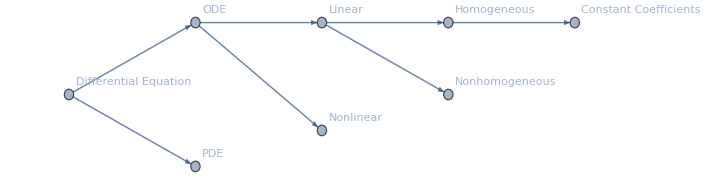

```mathematica
Graph[{1->2,2->5,1->3,4->7,2->4,4->6,6->8},]
```